```mathematica
(*graphics options*)
ptRad=.1;
(*Grid has (0,0) at the bottom left corner and (m-1,n-1) in the upper right*)
m=20;
n=20;
deletionCount=5;
deletionIndices=RandomSample[Table[i,{i,m*n}],deletionCount];
indexToGrid[i_]:={Mod[i-1,m],(i-1-Mod[i-1,m])/m};
gridToIndex[x_,y_]:=m*y+x+1;
```

```mathematica
A=ConstantArray[0,{m*n,m*n}];
For[a=0,a<m,a++,
For[b=0,b<n,b++,
current=gridToIndex[a,b];
right=gridToIndex[Mod[a+1,m],b];
left=gridToIndex[Mod[a-1,m],b];
below=gridToIndex[a,Mod[b-1,n]];
above=gridToIndex[a,Mod[b+1,n]];
If[!MemberQ[deletionIndices,right],A[[current]][[right]]=1.];
If[!MemberQ[deletionIndices,left],A[[current]][[left]]=1];
If[!MemberQ[deletionIndices,below],A[[current]][[below]]=1];
If[!MemberQ[deletionIndices,above],A[[current]][[above]]=1];
]
]
For[i=1,i≤Length[deletionIndices],i++,
A[[deletionIndices[[i]]]]=ConstantArray[0,m*n];
]
```

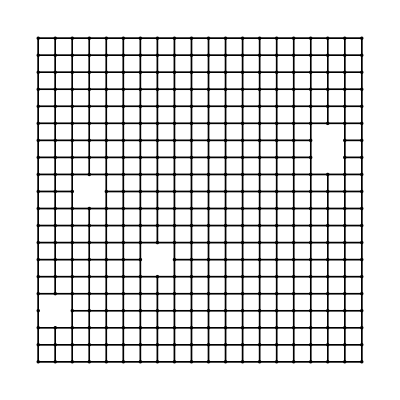

```mathematica
gridPoints={Black};
For[i=1,i≤Length[A],i++,
If[!MemberQ[deletionIndices,i],
AppendTo[gridPoints,Disk[indexToGrid[i],ptRad]]
]
]
gridLines={Black};
For[i=1,i≤Length[A],i++,
For[j=1,j≤Length[A],j++,
If[A[[i,j]]==1,
l={indexToGrid[i],indexToGrid[j]};
If[Norm[l[[2]]-l[[1]]]==1,
AppendTo[gridLines,Line[l]]
]
]
]
]
Show[Graphics[gridPoints],Graphics[gridLines]]
```

```mathematica
degreeCache=ConstantArray[0,m*n];
For[i=1,i≤Length[A],i++,
degreeCache[[i]]=Sum[A[[i,x]],{x,1,Length[A]}];
]
```

```mathematica
walkCount=200;
walkLength=10;
walks={};
For[i=1,i≤walkCount,i++,
curWalk={};
start=RandomInteger[{1,m*n}];
While[MemberQ[deletionIndices,start],
start=RandomInteger[{1,m*n}];
];
AppendTo[curWalk,indexToGrid[start]];
now=start;
For[j=1,j≤walkLength,j++,
nextChoices={};
nextWeights={};
For[k=1,k≤Length[A],k++,
If[A[[now,k]]==1,
AppendTo[nextChoices,k];
(*Approximation to MERW*)
AppendTo[nextWeights,N[Sum[A[[k,y]]*degreeCache[[y]],{y,1,Length[A]}]]];
]
];
nextWeights/=N[Sum[nextWeights[[z]],{z,1,Length[nextWeights]}]];
now=RandomChoice[nextWeights->nextChoices];
AppendTo[curWalk,indexToGrid[now]];
]
AppendTo[walks,curWalk];
]
grid={Opacity[.2],White};
For[i=1,i≤walkCount,i++,
For[j=1,j≤Length[walks[[i]]],j++,
AppendTo[grid,Point[walks[[i]][[j]]]]
]
]
Show[Graphics[Rectangle[indexToGrid[1],indexToGrid[m*n]]],Graphics[grid]]
```

$Aborted

Part::partw: Part 2 of {{{8, 12}, {8, 13}, {9, 13}, {9, 14}, {9, 15}, {10, 15}, {10, 14}, {10, 13}, {10, 14}, {10, 15}, {10, 14}}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-